# Nonlinear analysis of Rule 30

Alison Ord

## Abstract

The aim today (3 July 2019) is to compare and contrast results for rock4z and for Rule 30 of applying tools for nonlinear analysis.

Qualitatively, the first 1262 points (the same number as obtained for rock4z) described by Rule 30 display multifractal behaviour and long range correlations. Visually, the nonlinear results are remarkably similar to those for rock4z, far more similar than any of the mathematical models described in Ord et al. (2018; Figure 3, 4, 6 and 7. rock4z is Figure 6L, Broken Hill). Note that an attractor is well defined; its behaviour similar to rock4z not to that for white noise.

The next job is to pull together the quantitative results to compare with Tables 3 and 4 of Ord et al. (2018). Also, I still have to run SINDy on the data.

## Background

Compare and contrast (folded) rocks with Rule 30 in terms of a nonlinear dynamic system.

I attended Stephen Wolfram’s discussion session on 2 July 2019 regarding the Rule 30 Prize. It seems to me both appropriate and interesting to address the issue the way I know best, in terms of treating data from Rule 30 in the same manner as I have treated data (1D to date) from rocks.

Step 1 is to indeed treat data from Rule 30 exactly the same way I have to date treated rocks (1) so that it’s fast and (2) the results are directly comparable to what I have done so far (Ord and Hobbs 2018; Ord et al. 2018; and unpublished results).
  
  I have already used the Wolfram Language for some of these analyses, but I wish to use the Wolfram Language for all of these analyses, and interactively with the data and themselves so there may be feedback between the different forms of analysis providing an optimal nonlinear description of the data.
  
  Putting all this together I think is new, but the most important aspect is providing an easy to use tool from the nonlinear dynamical toolbox for geologists to explore their data in a completely new way.
  
  The use of the tool requires a pedagogic approach to its development. Some prioritisation will be required! Also, I have much data from other sources, 1 D, 2 D and 3 D, hyperspectral analyses, mechanical computational simulations created in external software, requiring this approach.

## The Data

### Rule 30

Copied from the Wolfram Documentation for CellularAutomaton 2July2019

Make a "random" walk from the values of cells on the center column of rule 30:

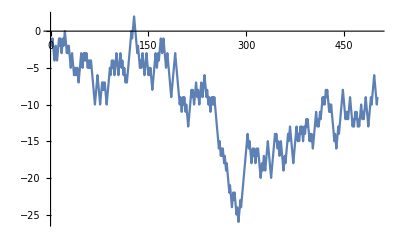

```mathematica
ListLinePlot[Accumulate[(-1)^CellularAutomaton[30,{{1},0},{500,{{0}}}]]]
```

Modifications for my purpose - 1262 points as that is the length of rock4z

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\Rule30Results"];
```

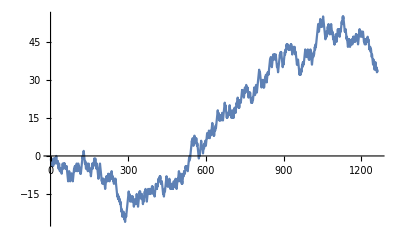

```mathematica
ListLinePlot[Accumulate[(-1)^CellularAutomaton[30,{{1},0},{1262,{{0}}}]]]
```

```mathematica
r30data=Accumulate[(-1)^CellularAutomaton[30,{{1},0},{1262,{{0}}}]];
```

```mathematica
%>>r30data
```

## The Analyses

### Spatial attractors

```mathematica
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx8192m"];
```

Here we show the spatial attractor for the data with a lag of 20, in various styles.

```mathematica
m=Import["r30datalag.xlsx",{"Sheets",2}];
ListPointPlot3D[m]
```

-Graphics3D-

```mathematica
ListPointPlot3D[m,DataRange->Automatic,ColorFunctionScaling->True,ColorFunction->"Rainbow",Axes->True,PlotRange->All,BoxRatios->{1,1,1},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
junk=BSplineCurve[{m}];
Tube[junk];
Graphics3D[{Orange,Specularity[White,10],Tube[junk,.2]},Axes->True,PlotRange->All,Boxed->True,BoxRatios->{1, 1, 1},BoxStyle->Directive[Dashed,Gray],Background->Black,LabelStyle->Directive[Black,Bold],AxesLabel->{t, t+5, t+10},ViewPoint->Front,ImagePadding->5]
```

-Graphics3D-

```mathematica
Graphics3D[{Yellow,Specularity[White,10],Tube[junk,.3]},Axes->True,PlotRange->All,Boxed->True,BoxRatios->{1, 1, 1},BoxStyle->Directive[Dashed,Gray],Background->Black,LabelStyle->Directive[Black,Bold],AxesLabel->{i, i+20, i+40},ViewPoint->Above,PreserveImageOptions->True,ImagePadding->5]
```

-Graphics3D-

```mathematica
Graphics3D[{Orange,Specularity[White,10],Tube[junk,.2]},Axes->True,PlotRange->All,Boxed->True,BoxRatios->{1, 1, 1},BoxStyle->Directive[Dashed,Gray],Background->Black,LabelStyle->Directive[Black,Bold],AxesLabel->{i, i+20,i+40},ViewPoint->{-2,2,0},ImagePadding->4]
```

-Graphics3D-

### Wavelet transforms

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\Rule30Results"]
data=ReadList["r30dataa"];
datalist=Flatten[data];
ListPlot[datalist,PlotRange->All,Joined->True]
```

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\Rule30Results

-Graphics-

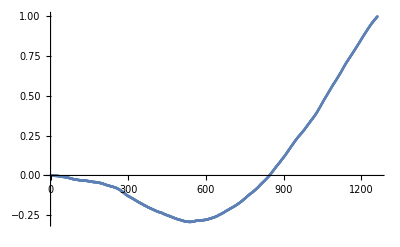

```mathematica
ListPlot[datalist];
ListPlot[Accumulate[datalist]];
Accumulate[datalist][[-1]];
ListPlot[Accumulate[datalist/%],GridLines->None]
```

ContinuousWaveletData[…]

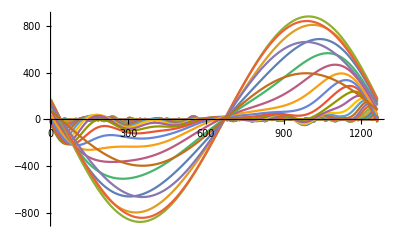

```mathematica
cwd=ContinuousWaveletTransform[datalist,WaveletScale->1]
cwd[All,"Values"];
recwd=Re[%];
cwd[{"WaveletScale","Octaves","Voices"}];
ListLinePlot[recwd,PlotRange->All]
```

```mathematica
cwd["Wavelet"];
{cwd["Scales"],cwd["WaveletScale"],cwd["WaveletIndex"]};
{cwd["LogScalogramFunction"],cwd["LinearScalogramFunction"]};
WaveletScalogram[cwd,ColorFunction->"CherryTones",Ticks->Full]
```

-Graphics-

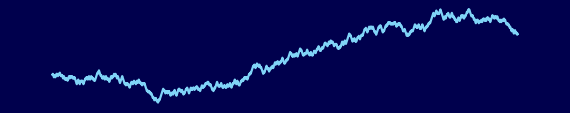
-Graphics-
-Graphics-

```mathematica
cf[x_]:=Blend[{RGBColor[0.,0.,0.3],RGBColor[0.,0.,0.5],RGBColor[0,0.1,0.5],RGBColor[0,0.2,1],RGBColor[0,0.5,1],RGBColor[0.2,0.7,1],RGBColor[0.5,0.8,1],RGBColor[0.5,.9,.9],RGBColor[0.5,1.,0.9],RGBColor[0.7,1,0.7],RGBColor[0.8,1,0.5],RGBColor[1,1,0],RGBColor[1,0.8,0],RGBColor[1,0.5,0],RGBColor[1,.25,0],RGBColor[1,.1,0.],RGBColor[1,.0,0.],RGBColor[.9,.0,0.],RGBColor[0.8,0.,0.],RGBColor[0.5,0.,0.],RGBColor[.25,0.,0.],RGBColor[0.1,0,0]},x];
Column[{ListLinePlot[datalist,Axes->None,ImageSize->570,AspectRatio->0.2,PlotRangePadding->None,PlotRange->All,Background->cf[0],PlotStyle->cf[0.3]],WaveletScalogram[cwd,ColorFunction->(cf[#]&),Axes->True,ImageSize->570,PlotRangePadding->None,Ticks->Full]},Spacings->0.2]
```

```mathematica
ListPlot3D[recwd,ColorFunction->"DarkRainbow",AxesLabel->{"depth","scale"},Mesh->None,PlotRange->All]
```

-Graphics3D-

Visualise a stationary wavelet transform using a common x axis plot . Mathematica featured example

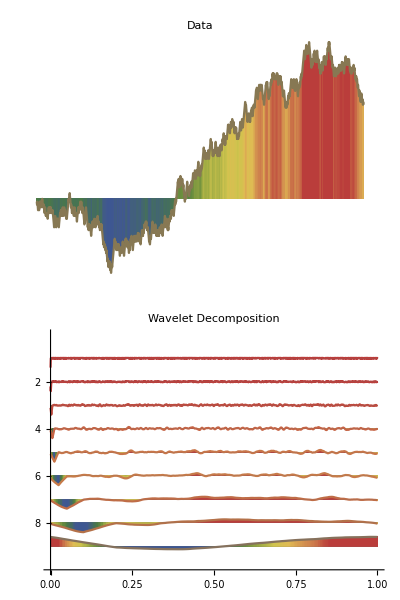

```mathematica
dwd=StationaryWaveletTransform[datalist,Automatic,8];
Column[{ListLinePlot[datalist,ImageSize->570,AspectRatio->0.2,Axes->None,ColorFunction->"DarkRainbow",Filling->Axis,PlotLabel->Style["Data",FontFamily->"Verdana",Brown,Bold,16],InterpolationOrder->2],WaveletListPlot[dwd,DataRange->{0,1},ColorFunction->"DarkRainbow",Filling->Axis,ImageSize->570,PlotRangePadding->None,TicksStyle->Directive[13,FontFamily->"Verdana"],PlotLabel->Style["Wavelet Decomposition",FontFamily->"Verdana",Brown,Bold,16]]}]
```

Visualise a stationary wavelet transform using a common y axis plot . Mathematica featured example

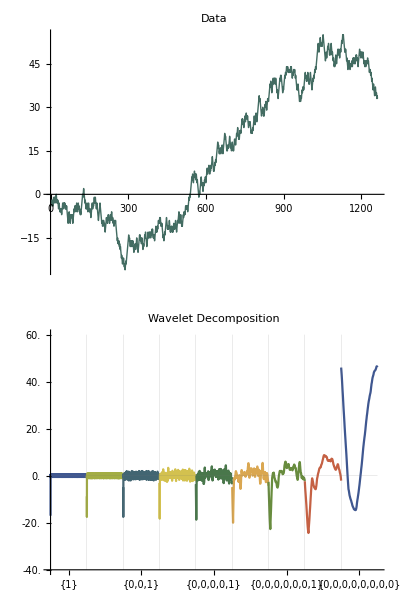

```mathematica
dwd=StationaryWaveletTransform[datalist,Automatic,8];
Column[{ListLinePlot[data,ImageSize->570,AspectRatio->0.2,PlotStyle->Directive[Thick,ColorData["DarkRainbow",0.2]],Axes->{False,True},TicksStyle->Directive[13,FontFamily->"Verdana"],PlotLabel->Style["Data",FontFamily->"Verdana",Brown,Bold,16],InterpolationOrder->2,ImagePadding->{{20,Automatic},{Automatic,Automatic}}],WaveletListPlot[dwd,Automatic,PlotStyle->(ColorData["DarkRainbow"]/@Riffle[#,#2]&@@Partition[Range[0.05,0.85,0.8/7],4]),ImageSize->570,PlotLayout->"CommonYAxis",Ticks->Full,TicksStyle->Directive[13,FontFamily->"Verdana"],PlotLabel->Style["Wavelet Decomposition",FontFamily->"Verdana",Brown,Bold,16],ImagePadding->{{30,Automatic},{Automatic,Automatic}}]},Alignment->Right]
```

### Singularity spectra

The singularity spectra are created using Last Wave. See Bacry et al. (1993) and Arneodo et al. (2008). I downloaded and modified the executable Demo code. I image someone is able to formulate it within mathematica - which would be a good thing to do. I take screen captures of the results and copy them into Powerpoint. Here’s the result for rock4z.

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\Rule30Results"];
imageshow=ImageResize[Import["r30data SingSpec.jpg"],Medium]
```

-Graphics-

### Hurst exponents

I developed the following while working towards understanding multiscaling and long range and anti correlations. At present, when I want to change a scale on a graph, I put the numbers in manually. Also, when the number of octaves changes, courtesy of a change in the number of data points, I put the numbers in manually. I feel sure mtca should be able to do this automatically for me, after a little thought. I have used the plots in at least 1 publication.
Note also that at present, I output the Hurst exponent per scale to corrgn1R, and then plot the Hurst exponents across scales externally within Excel. I feel sure I should be able to do this within mtca.

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\Rule30Results"];
data=ReadList["r30dataa"];
datalist=Flatten[data];
meandata=N[Mean[datalist]];
stddevndata=N[StandardDeviation[datalist]];
lengthdata=Length[datalist]
%>>corrgn1R;
```

1263

Second, determine the cumulative departures from the mean:

```mathematica
departmean=datalist-meandata;
accumdepartmean=Accumulate[departmean];
ListPlot[datalist,PlotRange->All];
ListPlot[accumdepartmean];
rangeaccumdepartmean=Max[accumdepartmean]-Min[accumdepartmean];
Flatten[Solve[rangeaccumdepartmean/stddevndata==(lengthdata/2)^x,x]]
x/. %
%>>>corrgn1R;
ListPlot[datalist,PlotRange->All,Joined->True]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.986166}

0.986166

-Graphics-

```mathematica
cwd=ContinuousWaveletTransform[datalist,WaveletScale->1]
cwd[All,"Values"];
recwd=Re[%];
cwd[{"WaveletScale","Octaves","Voices"}]
ListLinePlot[recwd,PlotRange->All]
```

ContinuousWaveletData[…]

{1,9,4}

-Graphics-

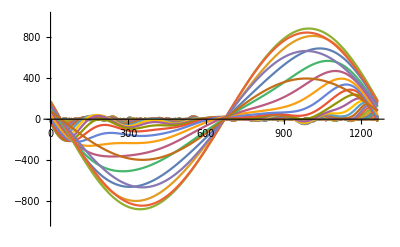

```mathematica
ListLinePlot[cwd[All,"Values"],PlotRange->{{0,1262},{-1000,1000}}]
```

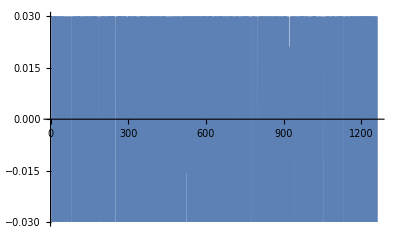

```mathematica
ListLinePlot[cwd[{1,1},"Values"],PlotRange->{{0,1262},{-.03,.03}}]
```

```mathematica
coeffts11=Re[Flatten[cwd[{1,1},"Values"]]];
meandatacoeffts11=Mean[coeffts11];
stddevndatacoeffts11=StandardDeviation[coeffts11];
lengthdatacoeffts11=Length[coeffts11];
departmeancoeffts11=coeffts11-meandatacoeffts11;
accumdepartmeancoeffts11=Accumulate[departmeancoeffts11];
rangeaccumdepartmeancoeffts11=Max[accumdepartmeancoeffts11]-Min[accumdepartmeancoeffts11];
Flatten[Solve[rangeaccumdepartmeancoeffts11/stddevndatacoeffts11==(lengthdatacoeffts11/2)^x,x]]
x/. %
%>>>corrgn1R;
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.534276}

0.534276

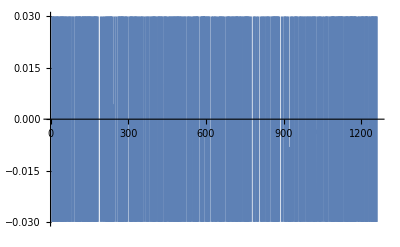

```mathematica
coeffts12=Re[Flatten[cwd[{1,2},"Values"]]];
ListLinePlot[cwd[{1,2},"Values"],PlotRange->{{0,1262},{-.03,.03}}]
```

```mathematica
;coeffts12>>corrgn1R_cwd_1_2;
```

```mathematica
meandatacoeffts12=Mean[coeffts12];
```

```mathematica
stddevndatacoeffts12=StandardDeviation[coeffts12];
```

```mathematica
lengthdatacoeffts12=Length[coeffts12];
```

```mathematica
departmeancoeffts12=coeffts12-meandatacoeffts12;
```

```mathematica
accumdepartmeancoeffts12=Accumulate[departmeancoeffts12];
```

```mathematica
rangeaccumdepartmeancoeffts12=Max[accumdepartmeancoeffts12]-Min[accumdepartmeancoeffts12];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts12/stddevndatacoeffts12==(lengthdatacoeffts12/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.548414}

```mathematica
x/. %
```

0.548414

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts13=Re[Flatten[cwd[{1,3},"Values"]]];
```

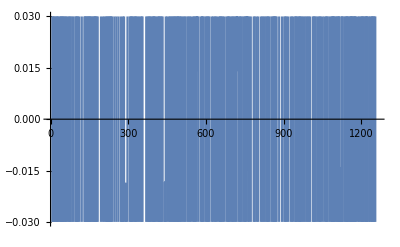

```mathematica
ListLinePlot[cwd[{1,3},"Values"],PlotRange->{{0,1262},{-.03,.03}}]
```

```mathematica
;coeffts13>>corrgn1R_cwd_1_3;
```

```mathematica
meandatacoeffts13=Mean[coeffts13];
```

```mathematica
stddevndatacoeffts13=StandardDeviation[coeffts13];
```

```mathematica
lengthdatacoeffts13=Length[coeffts13];
```

```mathematica
departmeancoeffts13=coeffts13-meandatacoeffts13;
```

```mathematica
accumdepartmeancoeffts13=Accumulate[departmeancoeffts13];
```

```mathematica
rangeaccumdepartmeancoeffts13=Max[accumdepartmeancoeffts13]-Min[accumdepartmeancoeffts13];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts13/stddevndatacoeffts13==(lengthdatacoeffts13/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.563126}

```mathematica
x/. %
```

0.563126

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts14=Re[Flatten[cwd[{1,4},"Values"]]];
```

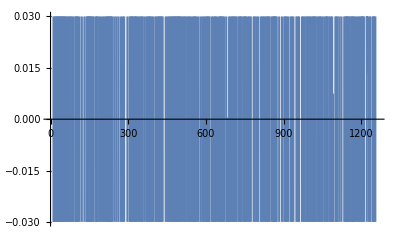

```mathematica
ListLinePlot[cwd[{1,4},"Values"],PlotRange->{{0,1262},{-.03,.03}}]
```

```mathematica
;coeffts12>>corrgn1R_cwd_1_4;
```

```mathematica
meandatacoeffts14=Mean[coeffts14];
```

```mathematica
stddevndatacoeffts14=StandardDeviation[coeffts14];
```

```mathematica
lengthdatacoeffts14=Length[coeffts14];
```

```mathematica
departmeancoeffts14=coeffts14-meandatacoeffts14;
```

```mathematica
accumdepartmeancoeffts14=Accumulate[departmeancoeffts14];
```

```mathematica
rangeaccumdepartmeancoeffts14=Max[accumdepartmeancoeffts14]-Min[accumdepartmeancoeffts14];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts14/stddevndatacoeffts14==(lengthdatacoeffts14/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.578821}

```mathematica
x/. %
```

0.578821

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts21=Re[Flatten[cwd[{2,1},"Values"]]];
```

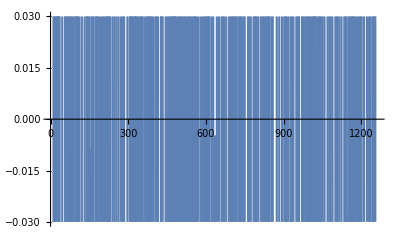

```mathematica
ListLinePlot[cwd[{2,1},"Values"],PlotRange->{{0,1262},{-.03,.03}}]
```

```mathematica
;coeffts21>>corrgn1R_cwd_2_1;
```

```mathematica
meandatacoeffts21=Mean[coeffts21];
```

```mathematica
stddevndatacoeffts21=StandardDeviation[coeffts21];
```

```mathematica
lengthdatacoeffts21=Length[coeffts21];
```

```mathematica
departmeancoeffts21=coeffts21-meandatacoeffts21;
```

```mathematica
accumdepartmeancoeffts21=Accumulate[departmeancoeffts21];
```

```mathematica
rangeaccumdepartmeancoeffts21=Max[accumdepartmeancoeffts21]-Min[accumdepartmeancoeffts21];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts21/stddevndatacoeffts21==(lengthdatacoeffts21/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.595307}

```mathematica
x/. %
```

0.595307

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts22=Re[Flatten[cwd[{2,2},"Values"]]];
```

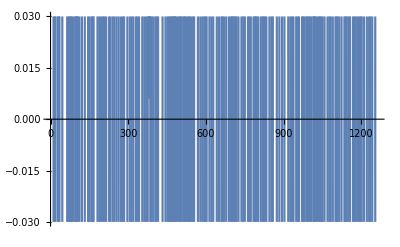

```mathematica
ListLinePlot[cwd[{2,2},"Values"],PlotRange->{{0,1262},{-.03,.03}}]
```

```mathematica
;coeffts22>>corrgn1R_cwd_2_2;
```

```mathematica
meandatacoeffts22=Mean[coeffts22];
```

```mathematica
stddevndatacoeffts22=StandardDeviation[coeffts22];
```

```mathematica
lengthdatacoeffts22=Length[coeffts22];
```

```mathematica
departmeancoeffts22=coeffts22-meandatacoeffts22;
```

```mathematica
accumdepartmeancoeffts22=Accumulate[departmeancoeffts22];
```

```mathematica
rangeaccumdepartmeancoeffts22=Max[accumdepartmeancoeffts22]-Min[accumdepartmeancoeffts22];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts22/stddevndatacoeffts22==(lengthdatacoeffts22/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.612109}

```mathematica
x/. %
```

0.612109

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts23=Re[Flatten[cwd[{2,3},"Values"]]];
```

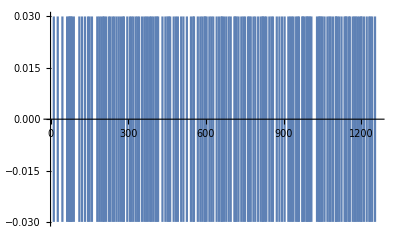

```mathematica
ListLinePlot[cwd[{2,3},"Values"],PlotRange->{{0,1262},{-.03,.03}}]
```

```mathematica
;coeffts23>>corrgn1R_cwd_2_3;
```

```mathematica
meandatacoeffts23=Mean[coeffts23];
```

```mathematica
stddevndatacoeffts23=StandardDeviation[coeffts23];
```

```mathematica
lengthdatacoeffts23=Length[coeffts23];
```

```mathematica
departmeancoeffts23=coeffts23-meandatacoeffts23;
```

```mathematica
accumdepartmeancoeffts23=Accumulate[departmeancoeffts23];
```

```mathematica
rangeaccumdepartmeancoeffts23=Max[accumdepartmeancoeffts23]-Min[accumdepartmeancoeffts23];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts23/stddevndatacoeffts23==(lengthdatacoeffts23/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.629068}

```mathematica
x/. %
```

0.629068

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts24=Re[Flatten[cwd[{2,4},"Values"]]];
```

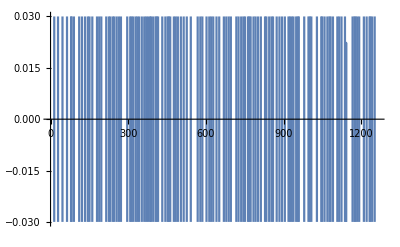

```mathematica
ListLinePlot[cwd[{2,4},"Values"],PlotRange->{{0,1262},{-.03,.03}}]
```

```mathematica
;coeffts24>>corrgn1R_cwd_2_4;
```

```mathematica
meandatacoeffts24=Mean[coeffts24];
```

```mathematica
stddevndatacoeffts24=StandardDeviation[coeffts24];
```

```mathematica
lengthdatacoeffts24=Length[coeffts24];
```

```mathematica
departmeancoeffts24=coeffts24-meandatacoeffts24;
```

```mathematica
accumdepartmeancoeffts24=Accumulate[departmeancoeffts24];
```

```mathematica
rangeaccumdepartmeancoeffts24=Max[accumdepartmeancoeffts24]-Min[accumdepartmeancoeffts24];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts24/stddevndatacoeffts24==(lengthdatacoeffts24/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.646139}

```mathematica
x/. %
```

0.646139

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts31=Re[Flatten[cwd[{3,1},"Values"]]];
```

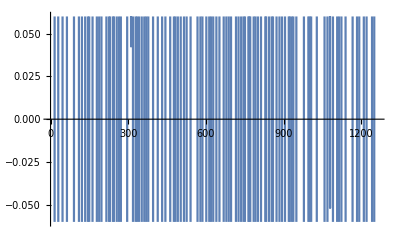

```mathematica
ListLinePlot[cwd[{3,1},"Values"],PlotRange->{{0,1262},{-.06,.06}}]
```

```mathematica
;coeffts31>>corrgn1R_cwd_3_1;
```

```mathematica
meandatacoeffts31=Mean[coeffts31];
```

```mathematica
stddevndatacoeffts31=StandardDeviation[coeffts31];
```

```mathematica
lengthdatacoeffts31=Length[coeffts31];
```

```mathematica
departmeancoeffts31=coeffts31-meandatacoeffts31;
```

```mathematica
accumdepartmeancoeffts31=Accumulate[departmeancoeffts31];
```

```mathematica
rangeaccumdepartmeancoeffts31=Max[accumdepartmeancoeffts31]-Min[accumdepartmeancoeffts31];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts31/stddevndatacoeffts31==(lengthdatacoeffts31/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.663404}

```mathematica
x/. %
```

0.663404

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts32=Re[Flatten[cwd[{3,2},"Values"]]];
```

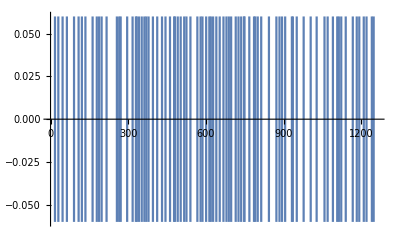

```mathematica
ListLinePlot[cwd[{3,2},"Values"],PlotRange->{{0,1262},{-.06,.06}}]
```

```mathematica
;coeffts32>>corrgn1R_cwd_3_2;
```

```mathematica
meandatacoeffts32=Mean[coeffts32];
```

```mathematica
stddevndatacoeffts32=StandardDeviation[coeffts32];
```

```mathematica
lengthdatacoeffts32=Length[coeffts32];
```

```mathematica
departmeancoeffts32=coeffts32-meandatacoeffts32;
```

```mathematica
accumdepartmeancoeffts32=Accumulate[departmeancoeffts32];
```

```mathematica
rangeaccumdepartmeancoeffts32=Max[accumdepartmeancoeffts32]-Min[accumdepartmeancoeffts32];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts32/stddevndatacoeffts32==(lengthdatacoeffts32/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.682025}

```mathematica
x/. %
```

0.682025

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts33=Re[Flatten[cwd[{3,3},"Values"]]];
```

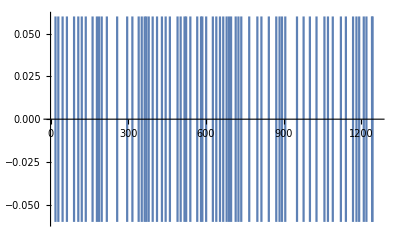

```mathematica
ListLinePlot[cwd[{3,3},"Values"],PlotRange->{{0,1262},{-.06,.06}}]
```

```mathematica
;coeffts33>>corrgn1R_cwd_3_3;
```

```mathematica
meandatacoeffts33=Mean[coeffts33];
```

```mathematica
stddevndatacoeffts33=StandardDeviation[coeffts33];
```

```mathematica
lengthdatacoeffts33=Length[coeffts33];
```

```mathematica
departmeancoeffts33=coeffts33-meandatacoeffts33;
```

```mathematica
accumdepartmeancoeffts33=Accumulate[departmeancoeffts33];
```

```mathematica
rangeaccumdepartmeancoeffts33=Max[accumdepartmeancoeffts33]-Min[accumdepartmeancoeffts33];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts33/stddevndatacoeffts33==(lengthdatacoeffts33/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.701947}

```mathematica
x/. %
```

0.701947

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts34=Re[Flatten[cwd[{3,4},"Values"]]];
```

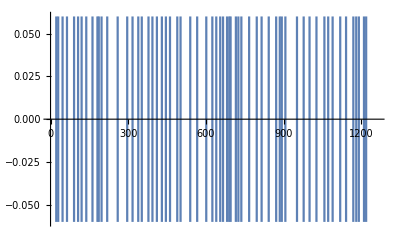

```mathematica
ListLinePlot[cwd[{3,4},"Values"],PlotRange->{{0,1262},{-.06,.06}}]
```

```mathematica
;coeffts34>>corrgn1R_cwd_3_4;
```

```mathematica
meandatacoeffts34=Mean[coeffts34];
```

```mathematica
stddevndatacoeffts34=StandardDeviation[coeffts34];
```

```mathematica
lengthdatacoeffts34=Length[coeffts34];
```

```mathematica
departmeancoeffts34=coeffts34-meandatacoeffts34;
```

```mathematica
accumdepartmeancoeffts34=Accumulate[departmeancoeffts34];
```

```mathematica
rangeaccumdepartmeancoeffts34=Max[accumdepartmeancoeffts34]-Min[accumdepartmeancoeffts34];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts34/stddevndatacoeffts34==(lengthdatacoeffts34/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.721579}

```mathematica
x/. %
```

0.721579

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts41=Re[Flatten[cwd[{4,1},"Values"]]];
```

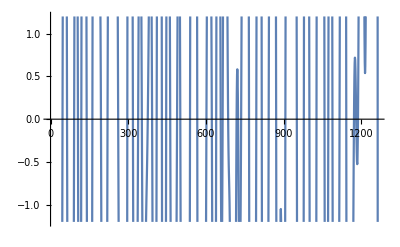

```mathematica
ListLinePlot[cwd[{4,1},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts41>>corrgn1R_cwd_4_1;
```

```mathematica
meandatacoeffts41=Mean[coeffts41];
```

```mathematica
stddevndatacoeffts41=StandardDeviation[coeffts41];
```

```mathematica
lengthdatacoeffts41=Length[coeffts41];
```

```mathematica
departmeancoeffts41=coeffts41-meandatacoeffts41;
```

```mathematica
accumdepartmeancoeffts41=Accumulate[departmeancoeffts41];
```

```mathematica
rangeaccumdepartmeancoeffts41=Max[accumdepartmeancoeffts41]-Min[accumdepartmeancoeffts41];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts41/stddevndatacoeffts41==(lengthdatacoeffts41/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.740482}

```mathematica
x/. %
```

0.740482

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts42=Re[Flatten[cwd[{4,2},"Values"]]];
```

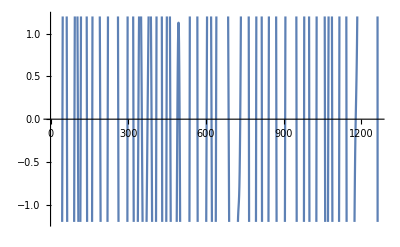

```mathematica
ListLinePlot[cwd[{4,2},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts42>>corrgn1R_cwd_4_2;
```

```mathematica
meandatacoeffts42=Mean[coeffts42];
```

```mathematica
stddevndatacoeffts42=StandardDeviation[coeffts42];
```

```mathematica
lengthdatacoeffts42=Length[coeffts42];
```

```mathematica
departmeancoeffts42=coeffts42-meandatacoeffts42;
```

```mathematica
accumdepartmeancoeffts42=Accumulate[departmeancoeffts42];
```

```mathematica
rangeaccumdepartmeancoeffts42=Max[accumdepartmeancoeffts42]-Min[accumdepartmeancoeffts42];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts42/stddevndatacoeffts42==(lengthdatacoeffts42/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.758329}

```mathematica
x/. %
```

0.758329

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts43=Re[Flatten[cwd[{4,3},"Values"]]];
```

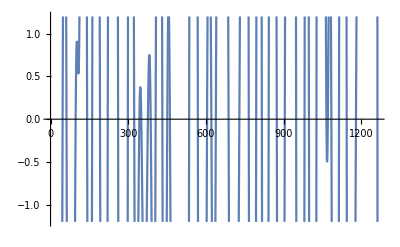

```mathematica
ListLinePlot[cwd[{4,3},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts43>>corrgn1R_cwd_4_3;
```

```mathematica
meandatacoeffts43=Mean[coeffts43];
```

```mathematica
stddevndatacoeffts43=StandardDeviation[coeffts43];
```

```mathematica
lengthdatacoeffts43=Length[coeffts43];
```

```mathematica
departmeancoeffts43=coeffts43-meandatacoeffts43;
```

```mathematica
accumdepartmeancoeffts43=Accumulate[departmeancoeffts43];
```

```mathematica
rangeaccumdepartmeancoeffts43=Max[accumdepartmeancoeffts43]-Min[accumdepartmeancoeffts43];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts43/stddevndatacoeffts43==(lengthdatacoeffts43/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.775698}

```mathematica
x/. %
```

0.775698

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts44=Re[Flatten[cwd[{4,4},"Values"]]];
```

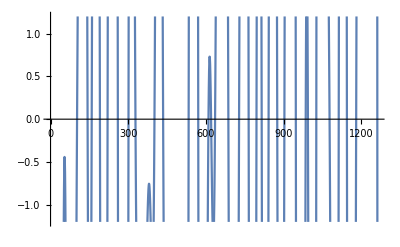

```mathematica
ListLinePlot[cwd[{4,4},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts44>>corrgn1R_cwd_4_4;
```

```mathematica
meandatacoeffts44=Mean[coeffts44];
```

```mathematica
stddevndatacoeffts44=StandardDeviation[coeffts44];
```

```mathematica
lengthdatacoeffts44=Length[coeffts44];
```

```mathematica
departmeancoeffts44=coeffts44-meandatacoeffts44;
```

```mathematica
accumdepartmeancoeffts44=Accumulate[departmeancoeffts44];
```

```mathematica
rangeaccumdepartmeancoeffts44=Max[accumdepartmeancoeffts44]-Min[accumdepartmeancoeffts44];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts44/stddevndatacoeffts44==(lengthdatacoeffts44/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.793803}

```mathematica
x/. %
```

0.793803

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts51=Re[Flatten[cwd[{5,1},"Values"]]];
```

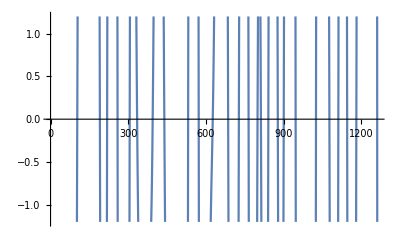

```mathematica
ListLinePlot[cwd[{5,1},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts51>>corrgn1R_cwd_5_1;
```

```mathematica
meandatacoeffts51=Mean[coeffts51];
```

```mathematica
stddevndatacoeffts51=StandardDeviation[coeffts51];
```

```mathematica
lengthdatacoeffts51=Length[coeffts51];
```

```mathematica
departmeancoeffts51=coeffts51-meandatacoeffts51;
```

```mathematica
accumdepartmeancoeffts51=Accumulate[departmeancoeffts51];
```

```mathematica
rangeaccumdepartmeancoeffts51=Max[accumdepartmeancoeffts51]-Min[accumdepartmeancoeffts51];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts51/stddevndatacoeffts51==(lengthdatacoeffts51/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.812956}

```mathematica
x/. %
```

0.812956

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts52=Re[Flatten[cwd[{5,2},"Values"]]];
```

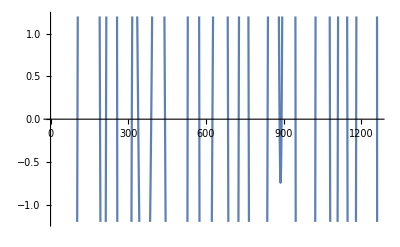

```mathematica
ListLinePlot[cwd[{5,2},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts52>>corrgn1R_cwd_5_2;
```

```mathematica
meandatacoeffts52=Mean[coeffts52];
```

```mathematica
stddevndatacoeffts52=StandardDeviation[coeffts52];
```

```mathematica
lengthdatacoeffts52=Length[coeffts52];
```

```mathematica
departmeancoeffts52=coeffts52-meandatacoeffts52;
```

```mathematica
accumdepartmeancoeffts52=Accumulate[departmeancoeffts52];
```

```mathematica
rangeaccumdepartmeancoeffts52=Max[accumdepartmeancoeffts52]-Min[accumdepartmeancoeffts52];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts52/stddevndatacoeffts52==(lengthdatacoeffts52/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.830366}

```mathematica
x/. %
```

0.830366

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts53=Re[Flatten[cwd[{5,3},"Values"]]];
```

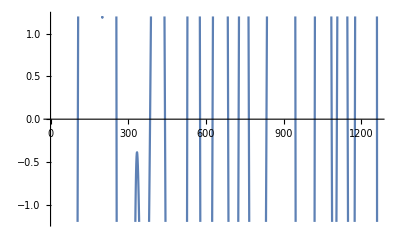

```mathematica
ListLinePlot[cwd[{5,3},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts53>>corrgn1R_cwd_5_3;
```

```mathematica
meandatacoeffts53=Mean[coeffts53];
```

```mathematica
stddevndatacoeffts53=StandardDeviation[coeffts53];
```

```mathematica
lengthdatacoeffts53=Length[coeffts53];
```

```mathematica
departmeancoeffts53=coeffts53-meandatacoeffts53;
```

```mathematica
accumdepartmeancoeffts53=Accumulate[departmeancoeffts53];
```

```mathematica
rangeaccumdepartmeancoeffts53=Max[accumdepartmeancoeffts53]-Min[accumdepartmeancoeffts53];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts53/stddevndatacoeffts53==(lengthdatacoeffts53/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.845575}

```mathematica
x/. %
```

0.845575

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts54=Re[Flatten[cwd[{5,4},"Values"]]];
```

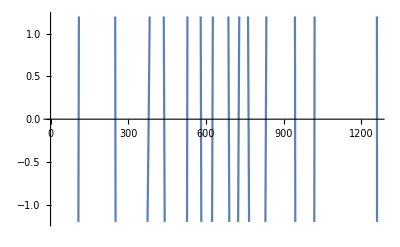

```mathematica
ListLinePlot[cwd[{5,4},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts54>>corrgn1R_cwd_5_4;
```

```mathematica
meandatacoeffts54=Mean[coeffts54];
```

```mathematica
stddevndatacoeffts54=StandardDeviation[coeffts54];
```

```mathematica
lengthdatacoeffts54=Length[coeffts54];
```

```mathematica
departmeancoeffts54=coeffts54-meandatacoeffts54;
```

```mathematica
accumdepartmeancoeffts54=Accumulate[departmeancoeffts54];
```

```mathematica
rangeaccumdepartmeancoeffts54=Max[accumdepartmeancoeffts54]-Min[accumdepartmeancoeffts54];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts54/stddevndatacoeffts54==(lengthdatacoeffts54/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.859946}

```mathematica
x/. %
```

0.859946

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts61=Re[Flatten[cwd[{6,1},"Values"]]];
```

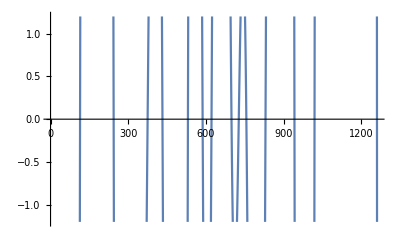

```mathematica
ListLinePlot[cwd[{6,1},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts61>>corrgn1R_cwd_6_1;
```

```mathematica
meandatacoeffts61=Mean[coeffts61];
```

```mathematica
stddevndatacoeffts61=StandardDeviation[coeffts61];
```

```mathematica
lengthdatacoeffts61=Length[coeffts61];
```

```mathematica
departmeancoeffts61=coeffts61-meandatacoeffts61;
```

```mathematica
accumdepartmeancoeffts61=Accumulate[departmeancoeffts61];
```

```mathematica
rangeaccumdepartmeancoeffts61=Max[accumdepartmeancoeffts61]-Min[accumdepartmeancoeffts61];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts61/stddevndatacoeffts61==(lengthdatacoeffts61/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.87499}

```mathematica
x/. %
```

0.87499

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts62=Re[Flatten[cwd[{6,2},"Values"]]];
```

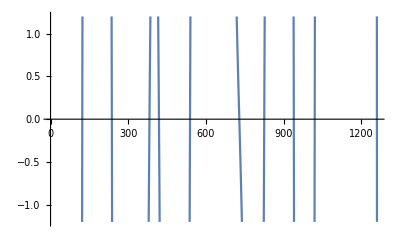

```mathematica
ListLinePlot[cwd[{6,2},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts62>>corrgn1R_cwd_6_2;
```

```mathematica
meandatacoeffts62=Mean[coeffts62];
```

```mathematica
stddevndatacoeffts62=StandardDeviation[coeffts62];
```

```mathematica
lengthdatacoeffts62=Length[coeffts62];
```

```mathematica
departmeancoeffts62=coeffts62-meandatacoeffts62;
```

```mathematica
accumdepartmeancoeffts62=Accumulate[departmeancoeffts62];
```

```mathematica
rangeaccumdepartmeancoeffts62=Max[accumdepartmeancoeffts62]-Min[accumdepartmeancoeffts62];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts62/stddevndatacoeffts62==(lengthdatacoeffts62/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.8919}

```mathematica
x/. %
```

0.8919

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts63=Re[Flatten[cwd[{6,3},"Values"]]];
```

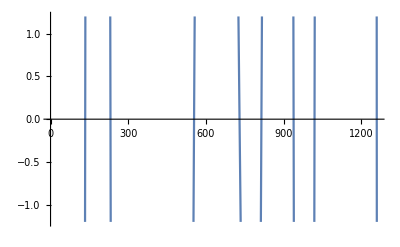

```mathematica
ListLinePlot[cwd[{6,3},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts63>>corrgn1R_cwd_6_3;
```

```mathematica
meandatacoeffts63=Mean[coeffts63];
```

```mathematica
stddevndatacoeffts63=StandardDeviation[coeffts63];
```

```mathematica
lengthdatacoeffts63=Length[coeffts63];
```

```mathematica
departmeancoeffts63=coeffts63-meandatacoeffts63;
```

```mathematica
accumdepartmeancoeffts63=Accumulate[departmeancoeffts63];
```

```mathematica
rangeaccumdepartmeancoeffts63=Max[accumdepartmeancoeffts63]-Min[accumdepartmeancoeffts63];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts63/stddevndatacoeffts63==(lengthdatacoeffts63/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.910969}

```mathematica
x/. %
```

0.910969

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts64=Re[Flatten[cwd[{6,4},"Values"]]];
```

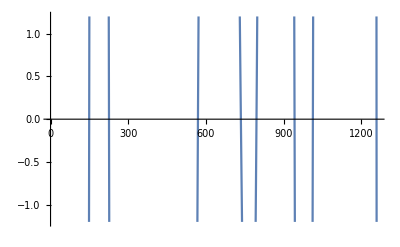

```mathematica
ListLinePlot[cwd[{6,4},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts64>>corrgn1R_cwd_6_4;
```

```mathematica
meandatacoeffts64=Mean[coeffts64];
```

```mathematica
stddevndatacoeffts64=StandardDeviation[coeffts64];
```

```mathematica
lengthdatacoeffts64=Length[coeffts64];
```

```mathematica
departmeancoeffts64=coeffts64-meandatacoeffts64;
```

```mathematica
accumdepartmeancoeffts64=Accumulate[departmeancoeffts64];
```

```mathematica
rangeaccumdepartmeancoeffts64=Max[accumdepartmeancoeffts64]-Min[accumdepartmeancoeffts64];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts64/stddevndatacoeffts64==(lengthdatacoeffts64/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.930449}

```mathematica
x/. %
```

0.930449

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts71=Re[Flatten[cwd[{7,1},"Values"]]];
```

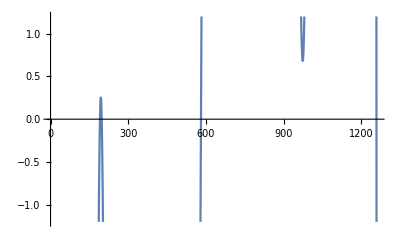

```mathematica
ListLinePlot[cwd[{7,1},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts71>>corrgn1R_cwd_7_1;
```

```mathematica
meandatacoeffts71=Mean[coeffts71];
```

```mathematica
stddevndatacoeffts71=StandardDeviation[coeffts71];
```

```mathematica
lengthdatacoeffts71=Length[coeffts71];
```

```mathematica
departmeancoeffts71=coeffts71-meandatacoeffts71;
```

```mathematica
accumdepartmeancoeffts71=Accumulate[departmeancoeffts71];
```

```mathematica
rangeaccumdepartmeancoeffts71=Max[accumdepartmeancoeffts71]-Min[accumdepartmeancoeffts71];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts71/stddevndatacoeffts71==(lengthdatacoeffts71/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.94803}

```mathematica
x/. %
```

0.94803

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts72=Re[Flatten[cwd[{7,2},"Values"]]];
```

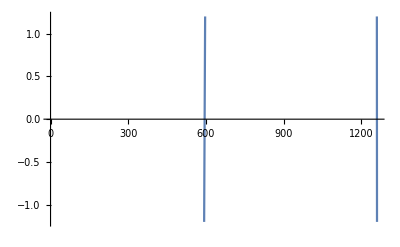

```mathematica
ListLinePlot[cwd[{7,2},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts72>>corrgn1R_cwd_7_2;
```

```mathematica
meandatacoeffts72=Mean[coeffts72];
```

```mathematica
stddevndatacoeffts72=StandardDeviation[coeffts72];
```

```mathematica
lengthdatacoeffts72=Length[coeffts72];
```

```mathematica
departmeancoeffts72=coeffts72-meandatacoeffts72;
```

```mathematica
accumdepartmeancoeffts72=Accumulate[departmeancoeffts72];
```

```mathematica
rangeaccumdepartmeancoeffts72=Max[accumdepartmeancoeffts72]-Min[accumdepartmeancoeffts72];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts72/stddevndatacoeffts72==(lengthdatacoeffts72/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.961925}

```mathematica
x/. %
```

0.961925

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts73=Re[Flatten[cwd[{7,3},"Values"]]];
```

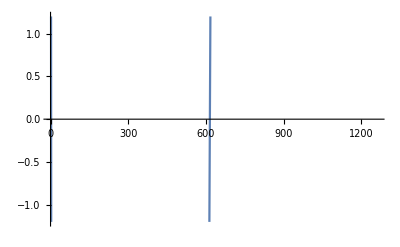

```mathematica
ListLinePlot[cwd[{7,3},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts73>>corrgn1R_cwd_7_3;
```

```mathematica
meandatacoeffts73=Mean[coeffts73];
```

```mathematica
stddevndatacoeffts73=StandardDeviation[coeffts73];
```

```mathematica
lengthdatacoeffts73=Length[coeffts73];
```

```mathematica
departmeancoeffts73=coeffts73-meandatacoeffts73;
```

```mathematica
accumdepartmeancoeffts73=Accumulate[departmeancoeffts73];
```

```mathematica
rangeaccumdepartmeancoeffts73=Max[accumdepartmeancoeffts73]-Min[accumdepartmeancoeffts73];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts73/stddevndatacoeffts73==(lengthdatacoeffts73/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.971175}

```mathematica
x/. %
```

0.971175

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts74=Re[Flatten[cwd[{7,4},"Values"]]];
```

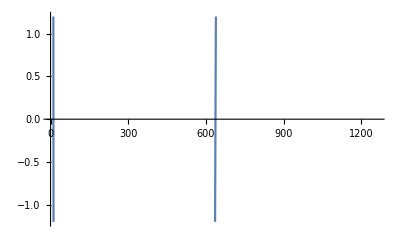

```mathematica
ListLinePlot[cwd[{7,4},"Values"],PlotRange->{{0,1262},{-1.2,1.2}}]
```

```mathematica
;coeffts74>>corrgn1R_cwd_7_4;
```

```mathematica
meandatacoeffts74=Mean[coeffts74];
```

```mathematica
stddevndatacoeffts74=StandardDeviation[coeffts74];
```

```mathematica
lengthdatacoeffts74=Length[coeffts74];
```

```mathematica
departmeancoeffts74=coeffts74-meandatacoeffts74;
```

```mathematica
accumdepartmeancoeffts74=Accumulate[departmeancoeffts74];
```

```mathematica
rangeaccumdepartmeancoeffts74=Max[accumdepartmeancoeffts74]-Min[accumdepartmeancoeffts74];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts74/stddevndatacoeffts74==(lengthdatacoeffts74/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.976454}

```mathematica
x/. %
```

0.976454

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts81=Re[Flatten[cwd[{8,1},"Values"]]];
```

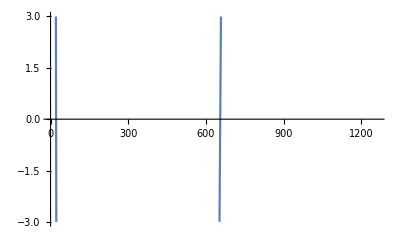

```mathematica
ListLinePlot[cwd[{8,1},"Values"],PlotRange->{{0,1262},{-3.,3.}}]
```

```mathematica
;coeffts81>>corrgn1R_cwd_8_1;
```

```mathematica
meandatacoeffts81=Mean[coeffts81];
```

```mathematica
stddevndatacoeffts81=StandardDeviation[coeffts81];
```

```mathematica
lengthdatacoeffts81=Length[coeffts81];
```

```mathematica
departmeancoeffts81=coeffts81-meandatacoeffts81;
```

```mathematica
accumdepartmeancoeffts81=Accumulate[departmeancoeffts81];
```

```mathematica
rangeaccumdepartmeancoeffts81=Max[accumdepartmeancoeffts81]-Min[accumdepartmeancoeffts81];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts81/stddevndatacoeffts81==(lengthdatacoeffts81/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.979355}

```mathematica
x/. %
```

0.979355

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts82=Re[Flatten[cwd[{8,2},"Values"]]];
```

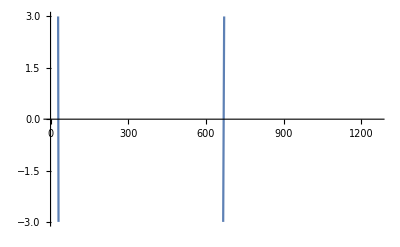

```mathematica
ListLinePlot[cwd[{8,2},"Values"],PlotRange->{{0,1262},{-3.,3.}}]
```

```mathematica
;coeffts82>>corrgn1R_cwd_8_2;
```

```mathematica
meandatacoeffts82=Mean[coeffts82];
```

```mathematica
stddevndatacoeffts82=StandardDeviation[coeffts82];
```

```mathematica
lengthdatacoeffts82=Length[coeffts82];
```

```mathematica
departmeancoeffts82=coeffts82-meandatacoeffts82;
```

```mathematica
accumdepartmeancoeffts82=Accumulate[departmeancoeffts82];
```

```mathematica
rangeaccumdepartmeancoeffts82=Max[accumdepartmeancoeffts82]-Min[accumdepartmeancoeffts82];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts82/stddevndatacoeffts82==(lengthdatacoeffts82/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.981272}

```mathematica
x/. %
```

0.981272

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts83=Re[Flatten[cwd[{8,3},"Values"]]];
```

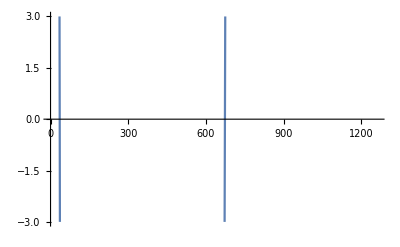

```mathematica
ListLinePlot[cwd[{8,3},"Values"],PlotRange->{{0,1262},{-3.,3.}}]
```

```mathematica
;coeffts83>>corrgn1R_cwd_8_3;
```

```mathematica
meandatacoeffts83=Mean[coeffts83];
```

```mathematica
stddevndatacoeffts83=StandardDeviation[coeffts83];
```

```mathematica
lengthdatacoeffts83=Length[coeffts83];
```

```mathematica
departmeancoeffts83=coeffts83-meandatacoeffts83;
```

```mathematica
accumdepartmeancoeffts83=Accumulate[departmeancoeffts83];
```

```mathematica
rangeaccumdepartmeancoeffts83=Max[accumdepartmeancoeffts83]-Min[accumdepartmeancoeffts83];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts83/stddevndatacoeffts83==(lengthdatacoeffts83/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.982636}

```mathematica
x/. %
```

0.982636

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts84=Re[Flatten[cwd[{8,4},"Values"]]];
```

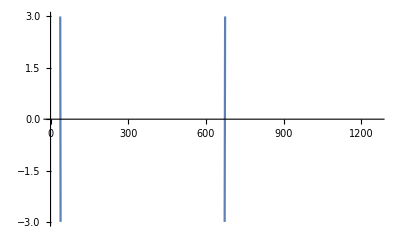

```mathematica
ListLinePlot[cwd[{8,4},"Values"],PlotRange->{{0,1262},{-3.,3.}}]
```

```mathematica
;coeffts84>>corrgn1R_cwd_8_4;
```

```mathematica
meandatacoeffts84=Mean[coeffts84];
```

```mathematica
stddevndatacoeffts84=StandardDeviation[coeffts84];
```

```mathematica
lengthdatacoeffts84=Length[coeffts84];
```

```mathematica
departmeancoeffts84=coeffts84-meandatacoeffts84;
```

```mathematica
accumdepartmeancoeffts84=Accumulate[departmeancoeffts84];
```

```mathematica
rangeaccumdepartmeancoeffts84=Max[accumdepartmeancoeffts84]-Min[accumdepartmeancoeffts84];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts84/stddevndatacoeffts84==(lengthdatacoeffts84/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.983372}

```mathematica
x/. %
```

0.983372

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts91=Re[Flatten[cwd[{9,1},"Values"]]];
```

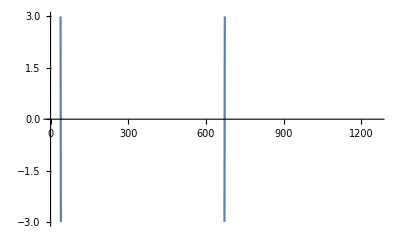

```mathematica
ListLinePlot[cwd[{9,1},"Values"],PlotRange->{{0,1262},{-3.,3.}}]
```

```mathematica
;coeffts91>>corrgn1R_cwd_9_1;
```

```mathematica
meandatacoeffts91=Mean[coeffts91];
```

```mathematica
stddevndatacoeffts91=StandardDeviation[coeffts91];
```

```mathematica
lengthdatacoeffts91=Length[coeffts91];
```

```mathematica
departmeancoeffts91=coeffts91-meandatacoeffts91;
```

```mathematica
accumdepartmeancoeffts91=Accumulate[departmeancoeffts91];
```

```mathematica
rangeaccumdepartmeancoeffts91=Max[accumdepartmeancoeffts91]-Min[accumdepartmeancoeffts91];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts91/stddevndatacoeffts91==(lengthdatacoeffts91/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.983612}

```mathematica
x/. %
```

0.983612

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts92=Re[Flatten[cwd[{9,2},"Values"]]];
```

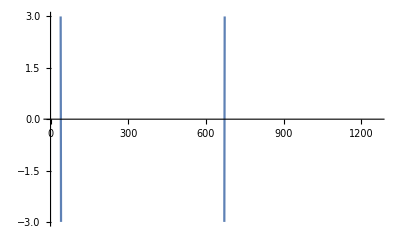

```mathematica
ListLinePlot[cwd[{9,2},"Values"],PlotRange->{{0,1262},{-3.,3.}}]
```

```mathematica
;coeffts92>>corrgn1R_cwd_9_2;
```

```mathematica
meandatacoeffts92=Mean[coeffts92];
```

```mathematica
stddevndatacoeffts92=StandardDeviation[coeffts92];
```

```mathematica
lengthdatacoeffts92=Length[coeffts92];
```

```mathematica
departmeancoeffts92=coeffts92-meandatacoeffts92;
```

```mathematica
accumdepartmeancoeffts92=Accumulate[departmeancoeffts92];
```

```mathematica
rangeaccumdepartmeancoeffts92=Max[accumdepartmeancoeffts92]-Min[accumdepartmeancoeffts92];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts92/stddevndatacoeffts92==(lengthdatacoeffts92/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.983651}

```mathematica
x/. %
```

0.983651

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts93=Re[Flatten[cwd[{9,3},"Values"]]];
```

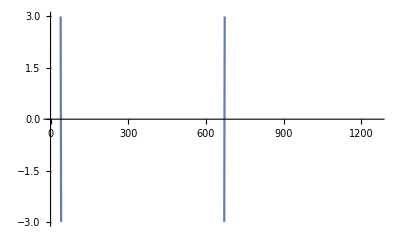

```mathematica
ListLinePlot[cwd[{9,3},"Values"],PlotRange->{{0,1262},{-3.,3.}}]
```

```mathematica
;coeffts93>>corrgn1R_cwd_9_3;
```

```mathematica
meandatacoeffts93=Mean[coeffts93];
```

```mathematica
stddevndatacoeffts93=StandardDeviation[coeffts93];
```

```mathematica
lengthdatacoeffts93=Length[coeffts93];
```

```mathematica
departmeancoeffts93=coeffts93-meandatacoeffts93;
```

```mathematica
accumdepartmeancoeffts93=Accumulate[departmeancoeffts93];
```

```mathematica
rangeaccumdepartmeancoeffts93=Max[accumdepartmeancoeffts93]-Min[accumdepartmeancoeffts93];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts93/stddevndatacoeffts93==(lengthdatacoeffts93/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.983653}

```mathematica
x/. %
```

0.983653

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts94=Re[Flatten[cwd[{9,4},"Values"]]];
```

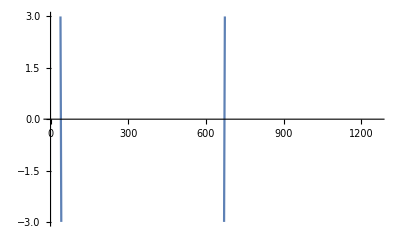

```mathematica
ListLinePlot[cwd[{9,4},"Values"],PlotRange->{{0,1262},{-3.,3.}}]
```

```mathematica
;coeffts94>>corrgn1R_cwd_9_4;
```

```mathematica
meandatacoeffts94=Mean[coeffts94];
```

```mathematica
stddevndatacoeffts94=StandardDeviation[coeffts94];
```

```mathematica
lengthdatacoeffts94=Length[coeffts94];
```

```mathematica
departmeancoeffts94=coeffts94-meandatacoeffts94;
```

```mathematica
accumdepartmeancoeffts94=Accumulate[departmeancoeffts94];
```

```mathematica
rangeaccumdepartmeancoeffts94=Max[accumdepartmeancoeffts94]-Min[accumdepartmeancoeffts94];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts94/stddevndatacoeffts94==(lengthdatacoeffts94/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.983653}

```mathematica
x/. %
```

0.983653

```mathematica
%>>>corrgn1R;
```

### Recurrence plots

Recurrence plots have been made using RQZ (Webber, 2012) and VRA (Kononov, 2006).
First, here is a screenshot from VRA with a dimension of 4 and a lag of 10

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\Rule30Results"];
imageshow=ImageResize[Import["r30data VRA.jpg"],Large]
```

-Graphics-

Second, here is a screenshot from RQA, with a dimension of 3 and a lag of 10

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\Rule30Results"];
imageshow=ImageResize[Import["r30data RQA.jpg"],Large]
```

-Graphics-

### Fourier transforms

### Recurrence histograms

Recurrence histograms are made using VRA (Kononov, 2006).
Here is a screenshot from VRA with a dimension of 4 and a lag of 20

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\Rule30Results"];
imageshow=ImageResize[Import["r30data VRA RecurrenceHistogram.jpg"],Large]
```

-Graphics-

### Networks

I have tried to use a mtca example, which uses a slider, but unfortunately, have not managed to go beyond that. I would like to!

### Discovery of physics from data

I would like to see where discussions on this topic might go.

#### Application of Brunton’s Matlab SINDy code using Octave

% Copyright 2018
% Code by Alison Ord based on Brunton et al. 2015
% based on rocks analysed in 2017/2018   JSG   PhilTransA

clear all, close all, clc
figpath = ‘../figures/’;
addpath(‘./utils’);
addpath(‘./data’);

%% generate Data
polyorder = 5;
usesine = 0;

n = 3;

% Integrate
% you need to load x as well as dx
load -ascii rock4z_x.txt
x=99*rock4z_x;
%N = length(x);
load -ascii rock4z_dx.txt
dx=217*rock4z_dx;
N = length(dx);

%% compute Derivative

%% pool Data  (i.e., build library of nonlinear time series)
Theta = poolData(x,n,polyorder,usesine);
m = size(Theta,2);

%% compute Sparse regression: sequential least squares
lambda = 0.025;      % lambda is our sparsification knob.
Xi = sparsifyDynamics(Theta,dx,lambda,n)
poolDataLIST({‘x’,’y’,’z’},Xi,n,polyorder,usesine);

Rock4z
Results of Sindy
﷐x﷯=0-0.12x+0.15y-0.03z                 should be xdot
﷐y﷯=0-0.04x+0.05y-0.09z             ydot
﷐z﷯=0+2.5x-7.2y+4.8z         zdot
    +0.05xx-0.07xy-0.05xz
    +0.03yy+0.03yz

% Copyright 2018, All Rights Reserved
% Code by Alison Ord based on Brunton et al. 2015
% For rock 4z  Ord&Hobbs 2018; Ord et al. 2018

clear all, close all, clc
figpath = ‘../figures/’;
addpath(‘./utils’);
addpath(‘./data’);

% orchid system
dt=.00001;
%x1 = 8; x2 = 9; x3 = 25;
%x1=0.001; x2=0.001; x3=0.001;
The choice of this is critical
x1=-0.001; x2=0.001; x3=-0.001

% Uses parameters derived thro’ Brunton’s code on rock4z
% x*220
for i = 500000 : 700000
x1 =  x1-0-(0.12*x1*dt)+(0.15*x2*dt)-(0.03*x3*dt);
x2 =  x2-0-(0.04*x1*dt)-(0.05*x2*dt)+(0.09*x3*dt);
x3 =  x3+0+(2.5*x1*dt)-(7.2*x2*dt)+(4.8*x3*dt)+(0.05*x1*x1*dt)-(0.07*x1*x2*dt)-(0.05*x1*x3*dt)+(0.03*x2*x2)+(0.03*x2*x3);
x(i,:) = [x1 x2 x3];
end

% plot phase space portrait
plot3(x(:,1),x(:,2),x(:,3))
grid, view(70,30)
xlabel(‘x_1’)
ylabel(‘x_2’)
zlabel(‘x_3’)

% plot variable over time
t = 0.01 : 0.01 : 1000;
plot(t,x(:,1))
xlabel(‘Time’)
ylabel(‘Velocity’)

% use only the first state and a time delay of six
tau = 6;
plot3(x(1:end-2*tau,1),x(1+tau:end-tau,1),x(1+2*tau:end,1))
grid, view([100 60])
xlabel(‘x_1’), ylabel(‘x_2’), zlabel(‘x_3’)

Results

```mathematica
image=Import["rock4zTimeSeries_3 i300k_600k.jpg"];
imageshow=ImageResize[image,Medium]
```

Import::nffil: File rock4zTimeSeries_3 i300k_600k.jpg not found during Import.

ImageResize::imginv: Expecting an image or graphics instead of $Failed.

ImageResize[$Failed,Medium]

```mathematica
image=Import["rock4zTimeSeries_3 i400k_500k.jpg"];
imageshow=ImageResize[image,Medium]
```

Import::nffil: File rock4zTimeSeries_3 i400k_500k.jpg not found during Import.

ImageResize::imginv: Expecting an image or graphics instead of $Failed.

ImageResize[$Failed,Medium]

### The vision is of moving a cursor through (x, y, z) coordinates for the surface of a deformed, folded rock and to watch data driven analyses change in different windows including : spatial attractors, wavelet transforms, singularity spectra, Hurst exponents, recurrence plots (including the ability for cross - and joint - recurrence plots and their quantitative analysis), Fourier transforms, recurrence histograms, networks, and sparsely determined nonlinear determinations of the differential equations describing the data.

#### References

Arneodo A, Audit B, Kestener P, Roux S. 2008 Wavelet-based multifractal analysis.
Scholarpedia 3, 4103. (doi:10.4249/scholarpedia.4103)
Bacry E, Muzy JF, Arneodo A. 1993 Singularity spectrum of fractal signals from wavelet
analysis: exact results. J. Stat. Phys. 70, 635–674. (doi:10.1007/BF01053588)
Brunton, S.L., Proctor, J.L., Kutz, J.N. 2015. Discovering governing equations from data: Sparse identification of nonlinear dynamical systems.  arXiv:1509.03580v1 
Brunton, S.L., Proctor, J.L., Kutz, J.N. 2016. Discovering governing equations from data by sparse identification of nonlinear dynamical systems. Proc. Natl. Acad. Sci. 113, 3932-3937.
Brunton, S.L., Noack, B.R., Koumoutsakos, P. 2019. Machine learning for fluid mechanics. arXiv:1905.11075v1
Champion, K., Zheng, P., Aravkin, A.Y., Brunton, S.L., Kutz, J.N. 2019 A unified sparse optimization framework to learn parsimonious physics-informed models from data. arXiv:1906.10612v1
da Silva, B., Higdon, D.M., Brunton, S.L.,  Kutz, J.N. 2019 Discovery of physics from data:Universal laws and discrepancy models. arXiv:1906.07906v1
Hobbs BE, Ord A. 2015 Structural geology: the mechanics of deforming metamorphic rocks.
Amsterdam, The Netherlands: Elsevier.
Hobbs, B.E., Ord, A. Nonlinear dynamical analysis of GNSS data: Quantification, precursors and synchronisation. Progress in Earth and Planetary Science. 2018. https://doi.org/10.1186/s40645-018-0193-6
Kononov E. 2006 VRA Visual Recurrence Analysis. Version 4.9. See http://web.archive.org/web/20070131023353 and http://www.myjavaserver.com/~nonlinear/vra/download.html.
Oberst, S., Niven, R.K., Lester, D.R., Ord, A., Hobbs, B. and Hoffmann, N. Detection of unstable periodic orbits in mineralising geological systems. Chaos 28, 085711 (2018); doi: 10.1063/1.5024134
Ord A. 1994 The fractal geometry of patterned structures in numerical models for rock
deformation. In Fractals and dynamic systems in geoscience (ed. JH Krühl), pp. 131–155. Berlin,
Germany: Springer.
Ord, A. and Hobbs, B.E. Quantitative measures of deformed rocks: the links to dynamics. Journal of Structural Geology, 2018. https://doi.org/10.1016/j.jsg.2018.05.027
Ord, A., Hobbs, B.E., Dering, G. and Gessner, K. Nonlinear analysis of natural folds using wavelet transforms and recurrence plots. Philosophical Transactions of the Royal Society A. 2018. http://dx.doi.org/10.1098/rsta.2017.0257	
Webber Jr CL. 2012 README_2012.PDF (Introduction to Recurrence Quantification Analysis, v 14.1). See http://homepages.luc.edu/~cwebber.
Wolfram Research, Inc., Mathematica, Version 12.0, Champaign, IL (2019).

Presentations

See the two presentations I have included in the reference directory. They provide an overview of our research, and some early results of using SINDy. They were designed for a general geology and minerals industry audience at the 2018 Australian Geological Congress in Adelaide. They were both well received, with standing room only.